200.

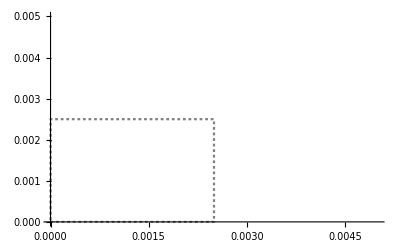

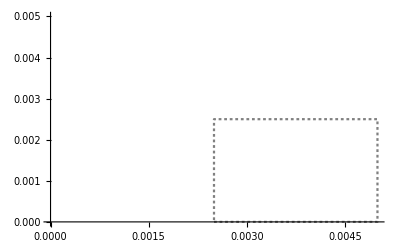

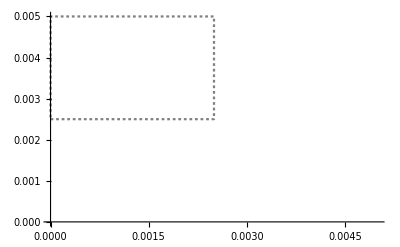

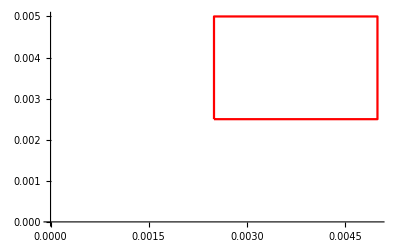

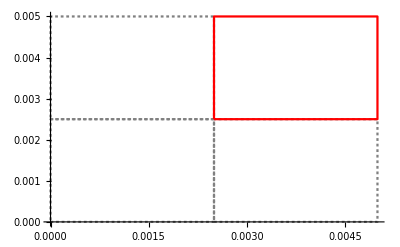

```mathematica
correction = 1/0.005

borderPoints = {{0, 0}, {0, 1}, {1, 1}, {1, 0}, {0, 0}};
ListLinePlot[borderPoints];

 leftBottom  = ListLinePlot[{{0, 0}, {0.5/correction, 0}, {0.5/correction, 0.5/correction}, {0, 0.5/correction}, {0, 0}}, PlotRange->{{0, 1/correction}, {0, 1/correction}}, PlotStyle->{Gray, Dashing[Tiny]}]
rightBottom  = ListLinePlot[{{0.5/correction, 0}, {1/correction, 0}, {1/correction, 0.5/correction}, {0.5/correction, 0.5/correction}, {0.5/correction, 0}}, PlotRange->{{0, 1/correction}, {0, 1/correction}}, PlotStyle->{Gray, Dashing[Tiny]}]
leftTop  = ListLinePlot[{{0, 0.5/correction}, {0.5/correction, 0.5/correction}, {0.5/correction, 1/correction}, {0, 1/correction}, {0, 0.5/correction}}, PlotRange->{{0, 1/correction}, {0, 1/correction}}, PlotStyle->{Gray, Dashing[Tiny]}]
rightTop  = ListLinePlot[{{0.5/correction, 0.5/correction}, {1/correction, 0.5/correction}, {1/correction, 1/correction}, {0.5/correction, 1/correction}, {0.5/correction, 0.5/correction}}, PlotRange->{{0, 1/correction}, {0, 1/correction}}, PlotStyle->Red]

allLines = Show[{leftBottom, rightBottom, leftTop, rightTop}]
```

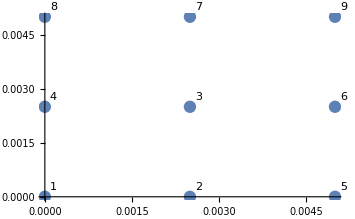

```mathematica
allPoints = {{0, 0,1}, {0.5/correction, 0,2}, {0.5/correction, 0.5/correction, 3}, {0, 0.5/correction, 4}, {1/correction, 0, 5}, {1/correction, 0.5/correction, 6}, {0.5/correction, 1/correction, 7}, {0, 1/correction, 8}, {1/correction, 1/correction, 9}};
allPointsPlot = ListPlot[Labeled[{#[[1]], #[[2]]},#[[3]]]&/@allPoints, PlotStyle -> PointSize[0.025]]
```

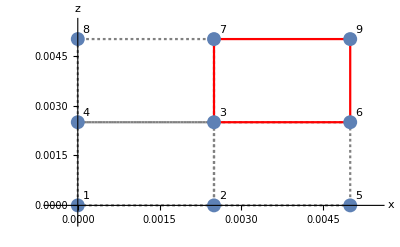

```mathematica
allPlot = Show[{leftBottom, rightBottom, leftTop, rightTop, allPointsPlot}, PlotRange->{{-0.1/correction, 1.1/correction}, {-0.1/correction, 1.1/correction}},AxesLabel->{"x","z"}]
```